```mathematica
ClearAll["Global`*"]
```

```mathematica
(*The Data has been taken from the following image. names of the variables are kept the same.*)
```

```mathematica
(*-Graphics--Graphics-*)
```

```mathematica
ep:={0.03,0.14,0.24,0.32,0.39,0.44,0.48,0.5,0.53,0.57}(*strains in compression, the -ve sign has been removed*)
```

```mathematica
ax:={1.53125,1.59375,1.84375,2.125,2.50000,2.93750,3.2500000,3.4687500,3.593750,3.640625}(*OK*)
```

```mathematica
ay:={0.1525,0.153250,0.15000,0.150,0.15125,0.17375,0.1971875,0.1990625,0.200625,0.200000}(*AK*)
```

```mathematica
b1:={1.46875,1.53125,1.750,2.000,2.34375,2.6875,3.031250, 3.21875,3.46875,3.59375}(*OL*)
```

```mathematica
b2:={1.40625,1.46875,1.625,1.875,2.17500,2.5000,2.796875, 3.00000,3.21875,3.46875}(*OM*)
```

```mathematica
c1:={0.00125,0.001875,0.0006250,0.00125,0.00125,0.00125,0.00000,0.0009375,0.001875,0.0009375}(*BC*)
```

```mathematica
c2:={0.05000,0.048750,0.0496875,0.02750,0.02625,0.02625,0.02625,0.0262500,0.048125,0.0750000}(*DE*)
```

```mathematica
d:={0.0525,0.051875,0.051,0.049275,0.1525,0.0265625,0.02625,0.02625,0.05,0.075}(*GH*)
```

```mathematica
e:={1.359375,1.478125,1.5,1.75,2.078125,2.375,2.671875,2.875,3.0625,3.375}(*ON*)
```

```mathematica
f:={0,0,0,0,0.0009375,0.023125,0.025,0.025625,0.046875,0.023125}(*IJ*)
```

```mathematica
{Length[ep],Length[ax],Length[ay],Length[b1],Length[b2],Length[c1],Length[c2],Length[d],Length[e],Length[f]}
```

{10,10,10,10,10,10,10,10,10,10}

```mathematica
-(-ay-c2-c1)[[9]]
```

0.250625

```mathematica
(c1+c2)*(ax+b2)/2
```

{0.0752734,0.0775195,0.0872607,0.0575,0.0642813,0.0747656,0.0793652,0.0879346,0.170313,0.269934}

```mathematica
c2*(b1+b2)/2
```

{0.071875,0.073125,0.0838477,0.0532813,0.0593086,0.0680859,0.0764941,0.0816211,0.160918,0.264844}

```mathematica
c1
```

{0.00125,0.001875,0.000625,0.00125,0.00125,0.00125,0.,0.0009375,0.001875,0.0009375}

```mathematica
c2
```

{0.05,0.04875,0.0496875,0.0275,0.02625,0.02625,0.02625,0.02625,0.048125,0.075}

```mathematica
c1+c2
```

{0.05125,0.050625,0.0503125,0.02875,0.0275,0.0275,0.02625,0.0271875,0.05,0.0759375}

## Extracting C(θ)

```mathematica
(*The objective here is to obtain C(θ) so that we can find ∫C(θ)dθ/Subscript[θ, c]*)
```

```mathematica
For[i=1,i<=Length[ep],i++,F[i_,θ_]:=Piecewise[{{ay[[i]]+c1[[i]]/(ax[[i]]-b1[[i]])*(ax[[i]]-θ),b1[[i]]<=θ<=ax[[i]]},{ay[[i]]+c1[[i]]+c2[[i]]/(b1[[i]]-b2[[i]])*(b1[[i]]-θ),b2[[i]]<=θ<=b1[[i]]},{ay[[i]]+c1[[i]]+c2[[i]],e[[i]]<=θ<=b2[[i]]}}];Backg[i_,θ_]:=ay[[i]]-f[[i]]/(ax[[i]]-e[[i]])*(ax[[i]]-θ)]
```

```mathematica
DC[jj_,x_]:=F[jj,x]-Backg[jj,x]
```

```mathematica
Manipulate[Plot[{F[jj,x],Backg[jj,x],DC[jj,x]},{x,e[[jj]],ax[[jj]]},PlotRange->{{1,3.7},{0,0.3}}],{jj,1,Length[ep],1}]
```

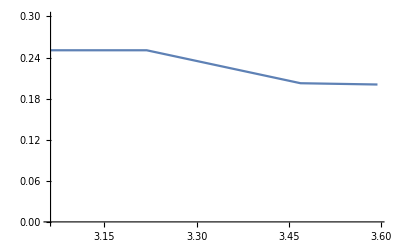

```mathematica
Plot[F[9,θ],{θ,e[[9]],ax[[9]]},PlotRange->{0,0.3}](*Testing*)
```

```mathematica
(*Here we compute C(θ)*)
```

```mathematica
Cp[jj_,x_]:=DC[jj,x]*x
```

```mathematica
Manipulate[Plot[{Cp[jj,x]},{x,e[[jj]],ax[[jj]]},PlotRange->{0,0.3}],{jj,1,Length[ep],1}]
```

```mathematica
(*Here we compute ∫(C(θ))/θ dθ:=Subscript[θ, c] Δη (change in entropy)*)
```

```mathematica
eta1[jj_]:=Integrate[Cp[jj,x],{x,e[[jj]],ax[[jj]]}]/((ax[[jj]]+b2[[jj]])/2)(*Integrating C(θ) in [e,ax], Subscript[θ, c]=(ax+b2)/2  *)
```

```mathematica
eta2[jj_]:=Integrate[Cp[jj,x],{x,b2[[jj]],ax[[jj]]}]/((ax[[jj]]+b2[[jj]])/2)(*Integrating C(θ) in [b2,ax], Subscript[θ, c]=(ax+b2)/2  *)
```

```mathematica
eta3[jj_]:=Integrate[DC[jj,x],{x,b2[[jj]],ax[[jj]]}](*Integrating Δη=\int C/θ dθ in [b2,ax]  *)
```

```mathematica
eta4[jj_]:=Integrate[DC[jj,x],{x,e[[jj]],ax[[jj]]}](*Integrating Δη=\int C/θ dθ in [e,ax]  *)
```

```mathematica
lambda1[jj_]:=Integrate[Cp[jj,x],{x,b2[[jj]],ax[[jj]]}](*Integrating C(θ) in [b2,ax] to get the latent heat  *)
```

```mathematica
Integrate[Cp[9,x],{x,b2[[9]],ax[[9]]}]/((ax[[9]]+b2[[9]])/2)(*TEST!!!*)
```

0.0125028

```mathematica
Manipulate[{eta1[jj],eta2[jj],eta3[jj],eta4[jj],Integrate[Cp[jj,x],{x,b2[[jj]],ax[[jj]]}],(ax[[jj]]+b2[[jj]])/2},{jj,1,Length[ep],1}]
```

```mathematica
ηη1=Range[Length[ep]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
ηη2=Range[Length[ep]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
ηη3=Range[Length[ep]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
ηη4=Range[Length[ep]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
ηη5=Range[Length[ep]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
λ1=Range[Length[ep]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
ηη1[[1]]=2;
```

```mathematica
ηη1
```

{2,2,3,4,5,6,7,8,9,10}

```mathematica
For[ii=1,ii<=Length[ep],ii++,ηη1[[ii]]=eta1[ii];ηη2[[ii]]=eta2[ii];ηη3[[ii]]=eta3[ii];ηη4[[ii]]=eta4[ii];λ1[[ii]]=lambda1[ii]]
```

```mathematica
For[i=1,i<=Length[ep],i++,ηη5[[i]]=((b1[[i]]-b2[[i]])*c2[[i]])/2+(b1[[i]]-b2[[i]])*c1[[i]]+((ax[[i]]-b1[[i]])*c1[[i]])/2+((ax[[i]]-e[[i]])*f[[i]])/2]
```

```mathematica
ηη1
```

{0.00389603,0.0012325,0.00875616,0.00513509,0.00502951,0.0119144,0.0127396,0.0133587,0.0254578,0.0146135}

```mathematica
ηη2
```

{0.00163425,0.00165617,0.00309034,0.00187826,0.00253279,0.00653129,0.00725366,0.0076715,0.0125028,0.00604339}

```mathematica
ηη3
```

{0.00167969,0.00169922,0.00321289,0.00195313,0.0026408,0.00678602,0.00751557,0.00793483,0.0128056,0.00611256}

```mathematica
ηη4
```

{0.00408203,0.00125889,0.00950195,0.00554688,0.00538525,0.012793,0.013584,0.0141992,0.0268652,0.0150171}

```mathematica
ηη5
```

{0.00167969,0.00169922,0.00321289,0.00195313,0.00272119,0.00935547,0.0103027,0.0108008,0.0190527,0.00789795}

```mathematica
λ1
```

{0.00240031,0.00253601,0.0053598,0.00375651,0.0059204,0.0177569,0.021931,0.0248125,0.0425876,0.0214824}

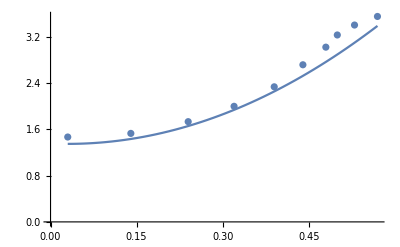

```mathematica
plt11=ListPlot[Transpose@{ep,(ax+b2)/2}];(*Transition temp vs strain*)
plt12=Plot[{1.35+7.0*(x-ep[[1]])^2},{x,ep[[1]],ep[[Length[ep]]]}];
Show[plt11,plt12]
```

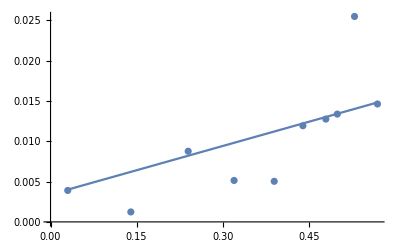

```mathematica
plt21=ListPlot[Transpose@{ep,ηη1}];(*entropy vs strain*)
plt22=Plot[{0.004+0.02*(x-ep[[1]])},{x,ep[[1]],ep[[Length[ep]]]}];(*integrating little beyond the peak.*)
Show[plt21,plt22]
```

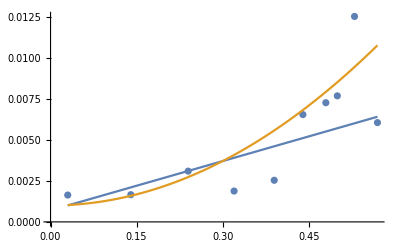

```mathematica
plt31=ListPlot[Transpose@{ep,ηη2}];(*entropy vs strain*)
plt32=Plot[{0.0010+0.01*(x-ep[[1]]),0.0010+0.03*(x-0ep[[1]])^2},{x,ep[[1]],ep[[Length[ep]]]}];(*integrating till the peak.*)
Show[plt31,plt32]
```

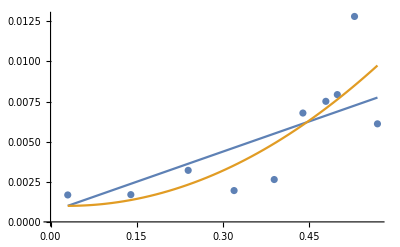

```mathematica
plt41=ListPlot[Transpose@{ep,ηη3}];(*entropy vs strain*)
plt42=Plot[{0.0010+0.0125*(x-ep[[1]]),0.0010+0.03*(x-ep[[1]])^2},{x,ep[[1]],ep[[Length[ep]]]}];(*integrating till the peak.*)
Show[plt41,plt42]
```

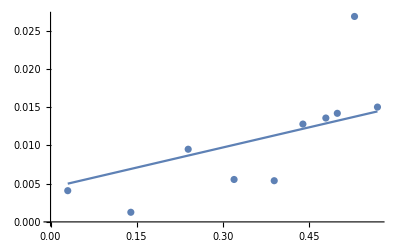

```mathematica
plt51=ListPlot[Transpose@{ep,ηη4}];(*entropy vs strain*)
plt52=Plot[{0.0050+0.0175*(x-ep[[1]])},{x,ep[[1]],ep[[Length[ep]]]}];(*integrating till the peak.*)
Show[plt51,plt52]
```

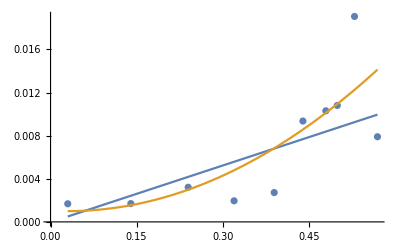

```mathematica
plt61=ListPlot[Transpose@{ep,ηη5}];(*entropy vs strain*)
plt62=Plot[{0.00050+0.0175*(x-ep[[1]]),0.0010+0.045*(x-ep[[1]])^2},{x,ep[[1]],ep[[Length[ep]]]}];(*integrating till the peak.*)
Show[plt61,plt62]
```

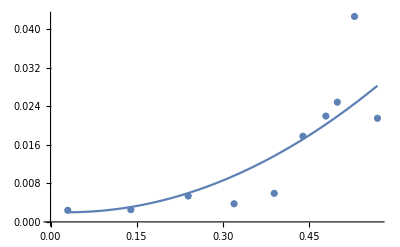

```mathematica
plt71=ListPlot[Transpose@{ep,λ1}];(*Transition temp vs strain*)
plt72=Plot[{0.002+0.09*(x-ep[[1]])^2},{x,ep[[1]],ep[[Length[ep]]]}];
Show[plt71,plt72]
```

## Trying to guess dσ/dθ_c

```mathematica
(*From Claussius clayperon eqn, we have dσ/Subscript[dθ, c]=Δη/(Subscript[ϵ, 2]-Subscript[ϵ, 1]). If we set Subscript[ϵ, 2]=0.6 and Subscript[ϵ, 1]=0.03, we get a plot for the rate of applied stress as*)
```

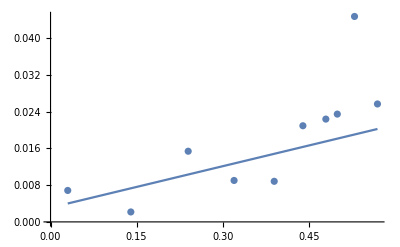

```mathematica
plt51=ListPlot[Transpose@{ep,ηη1/0.57}];(*entropy vs strain*)
plt52=Plot[{0.0040+0.03*(x-ep[[1]])},{x,ep[[1]],ep[[Length[ep]]]}];(*integrating till the peak.*)
Show[plt51,plt52]
```

```mathematica
(*To test the accuracy, we Take the ratio of the two*)
```

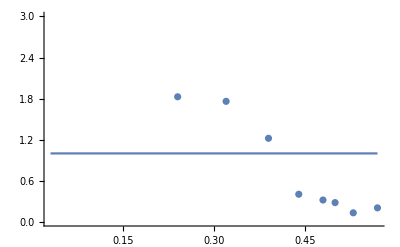

```mathematica
plt61=ListPlot[Transpose@{ep,10^-3/(ηη4*ep^2)}];(*entropy vs strain*)
plt62=Plot[{1},{x,ep[[1]],ep[[Length[ep]]]}];(*integrating till the peak.*)
Show[plt61,plt62,PlotRange->{0,3}]
```

```mathematica
10^-3/(ηη4[[1]]*ep[[1]]^2)
```

272.196

```mathematica
Figures used for Calculation
```

Calculation Figures for used

```mathematica
(*<ϵ=0%>*)
```

-Graphics-

```mathematica
(*<ϵ=-0.14%>*)
```

-Graphics-

```mathematica
(*<ϵ=-0.24%>*)
```

-Graphics-

```mathematica
(*<ϵ=-0.32>*)
```

-Graphics-

```mathematica
(*<ϵ=-0.39%>*)
```

-Graphics-

```mathematica
(*<ϵ=-0.44%>*)
```

-Graphics-

```mathematica
(*<ϵ=-0.48%>*)
```

-Graphics-

```mathematica
(*<ϵ=-0.50>*)
```

-Graphics-

```mathematica
(*<ϵ=-0.53%>*)
```

-Graphics-

```mathematica
(*<ϵ=-0.57%>*)
```

-Graphics-